# QES Velocity Curve

## Boxes

```mathematica
MakeBoxes[τ1,StandardForm]:=SubscriptBox["τ","1"];
MakeExpression[SubscriptBox["τ","1"],StandardForm]:=MakeExpression["τ1",StandardForm];
MakeBoxes[solarMass,StandardForm]:=SubscriptBox["M","☉"];
MakeExpression[SubscriptBox["M","☉"],StandardForm]:=MakeExpression["solarMass",StandardForm];MakeBoxes[acceleration,StandardForm]:=SubscriptBox["a","3"];
MakeExpression[SubscriptBox["a","3"],StandardForm]:=MakeExpression["acceleration",StandardForm];
MakeBoxes[v3,StandardForm]:=SubscriptBox["v","3"];
MakeExpression[SubscriptBox["v","3"],StandardForm]:=MakeExpression["v3",StandardForm];
```

## Units

```mathematica
s=1;
m=1;
cm=0.01 m;
kg=1;
g=0.001 kg;
J=(kg m^2)/s^2;
K=1;
km=1000 m;
yr=60 60 24 365.25 s;
kyr=1000 yr;
Myr=1000 kyr;
Gyr=1000 Myr;
M_☉=1.9891×10^30 kg;
pc=3.08567758 10^13 km;
kpc=1000 pc;
Mpc=1000 kpc;
Gpc=1000 Mpc;
```

## Constants

```mathematica
G=6.67408 10^-11 m^3/(kg s^2);
c=2.99792458×10^8 m/s;
```

## Clear Variables

```mathematica
ClearAll[Subscript[v, 3],Subscript[a, 3],Subscript[τ, 1],coreMass,coreRadius,V,ρ,M,vQ,vN]
```

### QES Constants

```mathematica
Subscript[v, 3]=2.790479×10^8;
Subscript[a, 3]=3.646616×10^-11;
Subscript[τ, 1]=5.688726×10^17;
```

```mathematica
coreMass=1.0×10^11 M_☉;
coreRadius=4kpc;
```

```mathematica
V[r_]=4/3 π r^3;
```

```mathematica
ρ=coreMass/V[coreRadius];
```

```mathematica
M[r_]:=If[r>coreRadius,coreMass,V[r]ρ];
```

```mathematica
vQ[r_]=√((M[r] G)/r+Subscript[a, 3] r);
vN[r_]=√((M[r] G)/r);
```

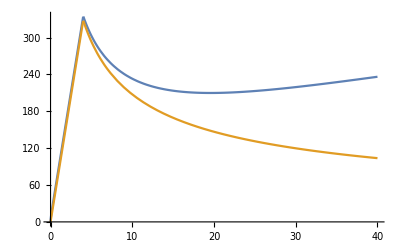

```mathematica
Plot[{vQ[r kpc]/km,vN[r kpc]/km},{r,0,40}]
```